```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Representation of Spatial Functions

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

```mathematica
TableForm[{{Hyperlink["AffineMap",{"vvInterp.nb","labelAffineMap"},BaseStyle->mathColor],labelAffineMap}}]
```

| A general linear function can stretch, flip, rotate, and translate the image

This notebook chronicles the further adventures of ImageTransformation[ ] and its cousins RotationTransform[ ], ReflectionTransform[ ], TranslationTransform[ ], and AffineTransform[ ].

At first it might seem strange that linear and affine functions on images are represented as 3-by-3 matrices. For instance, all of the named transformations

```mathematica
{RotationTransform[θ],ReflectionTransform[{1,-1}],TranslationTransform[{x,y}],AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}]}
```

{TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],TransformationFunction[(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)],TransformationFunction[(1 | 0 | x
0 | 1 | y
0 | 0 | 1)],TransformationFunction[(a11 | a12 | b1
a21 | a22 | b2
0 | 0 | 1)]}

have the form of a 2-by-2 “A” matrix, a 2-by-1 “B” column vector and a bottom row consisting of {0,0,1}. This is just a more convenient representation for the standard affine mapping y = Ax+b where A is the 2-by-2 matrix and B is the same 2-by-1 vector. To see this, let

```mathematica
a={{a11,a12},{a21,a22}};
b={b1,b2};
Row[{MatrixForm[a],Spacer[50],MatrixForm[b]}]
```

(a11 | a12
a21 | a22)(b1
b2)

A generic vector x={x1,x2} can be mapped through this affine transformation to give

```mathematica
y=a.{x1,x2}+b;
MatrixForm[y]
```

(b1+a11 x1+a12 x2
b2+a21 x1+a22 x2)

Using the general AffineTransformation[ ] function above, this can be implemented

```mathematica
t=AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}];
t[{x1,x2}]//MatrixForm
```

(b1+a11 x1+a12 x2
b2+a21 x1+a22 x2)

which is equal to y. To see what’s happening, rewrite each vector augmenting the dimensions by adding “1” so that x={x1,x2,1}. Grabbing the matrix out of the TransformationFunction wrapper shows that

```mathematica
tMat=TransformationMatrix[t];
MatrixForm[tMat]
```

(a11 | a12 | b1
a21 | a22 | b2
0 | 0 | 1)

and hence

```mathematica
tMat.{x1,x2,1}//MatrixForm
```

(b1+a11 x1+a12 x2
b2+a21 x1+a22 x2
1)

is the same as y with a “1” added to the bottom

```mathematica
Flatten[{y,1}]//MatrixForm
```

(b1+a11 x1+a12 x2
b2+a21 x1+a22 x2
1)

Transformation Functions such as AffineTransform[ ] can be applied directly to geometric objects: here is a blue circle mapped by a more or less arbitrarily chosen AffineTransformation[ ]

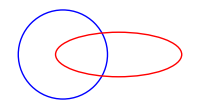

```mathematica
Graphics[{Blue,Circle[],Red,GeometricTransformation[Circle[],AffineTransform[{{{1,0},{-1,1/2}},{1.25,0}}]]},ImageSize->200]
```

```mathematica
iOld=1;
labelAffineMap="A general linear function can stretch, flip, rotate, and translate the image";
infoAffineMap="A general affine transformation has six parameters, and can accomplish rotations, shears, translations, and reflections. Play with the coefficients:\n\nThe b parameters translate (shift) the image left/right and up/down\n\nThe a parameters do the bulk of the work.\n\nFind a set of a's that cause the image to be flipped.\n\nFinf a set of a's that rotate the image.\n\nIf the image area is all black, press rest to return to the identity map.";
Manipulate[If[i≠iOld,reset=1;iOld=i;];
If[reset==1,a={1,0};a2={0,1};b={0,0};reset=0;];
Show[ImageTransformation[img=allImagesColor[[i]],AffineTransform[{{a,a2},b}]],ImageSize->500],
Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoAffineMap]}],Row[{Control[{{a,{1,0}},{-1,-1},{1,1}}],
Control[{{a2,{0,1},""},{-1,-1},{1,1}}],Spacer[20],
Control[{{b,{0,0}},{-1,-1},{1,1}}],Spacer[20],
Control[{reset,{0,1},ControlType->Checkbox}],Spacer[20],Dynamic[MatrixForm[{{a[[1]],a[[2]],b[[1]]},{a2[[1]],a2[[2]],b[[2]]},{0,0,1}}]]}],
FrameLabel->Style[labelAffineMap,Medium],TrackedSymbols->{i,a,a2,b,reset},SaveDefinitions->saveDef]
```

### Undoing Geometric Distortions: A Case Study

This notebook discusses by example how distortions can be identified and undone if suitable points of alignment can be found. This can be used to adjust for distortion caused by the lens of a camera, or to align two pictures using corresponding points in the two images. Suppose that the original image f[x,y] is subject to a geometric distortion yielding g[x’,y’]. Define a linear coordinate transformation function

```mathematica
tfX[x_,y_]:=a11 x+a12 y+b1;
tfY[x_,y_]:=a21 x+a22 y+b2;
```

With three pairs of points, this is a system of 6 equations and 6 unknowns, and so it is possible to solve for the as and bs, creating a mapping that “undoes” the effect of the distortion.

```mathematica
Image[-Graphics-,ImageSize->300]
```

-Graphics-

```mathematica
m[x1_,y1_,x2_,y2_,x3_,y3_]:={{x1,y1,1,0,0,0},{0,0,0,x1,y1,1},{x2,y2,1,0,0,0},{0,0,0,x2,y2,1},{x3,y3,1,0,0,0},{0,0,0,x3,y3,1}};
z={"x1'","y1'","x2'","y2'","x3'","y3'"};
Row[{MatrixForm[m[x1,y1,x2,y2,x3,y3]],MatrixForm[{a11,a12,b1,a21,a22,b2}],"=",MatrixForm[z]}]
```

(x1 | y1 | 1 | 0 | 0 | 0
0 | 0 | 0 | x1 | y1 | 1
x2 | y2 | 1 | 0 | 0 | 0
0 | 0 | 0 | x2 | y2 | 1
x3 | y3 | 1 | 0 | 0 | 0
0 | 0 | 0 | x3 | y3 | 1)(a11
a12
b1
a21
a22
b2)=(x1'
y1'
x2'
y2'
x3'
y3')

Rewriting this as m.c=z allows it to be solved for the unknowns as c=Inverse[m].z. In the standard form of a linear transformation, the cs would be rearranged to form the matrix

```mathematica
AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}]
```

TransformationFunction[(a11 | a12 | b1
a21 | a22 | b2
0 | 0 | 1)]

which can be applied to geometric objects or to images as above.

HW: Suppose that instead of three corresponding points, there were four pairs of points that are known to correspond. Generalize the above scheme to handle this case.